1 - 6 RLC-Circuits: special cases

1. RC-Circuit. Model the RC-Circuit in the figure below. Find the current due to a constant E.

```mathematica
Clear["Global`*"]
```

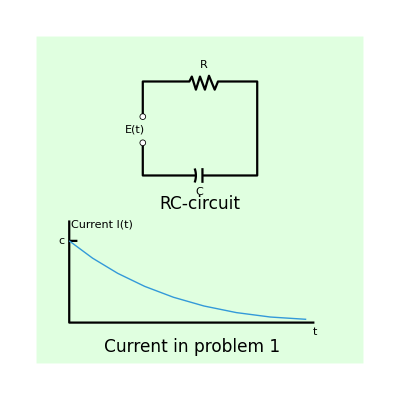

```mathematica
Graphics[{{LightGreen,Rectangle[{0,0},{4,4}]},{Thickness[0.004],Line[{{1.3,2.7},{1.3,2.3},{1.95,2.3}}]},{Thickness[0.004],Circle[{1.7,2.3},0.25,{-0.35,0.35}]},{Thickness[0.004],Line[{{2.03,2.3},{2.7,2.3},{2.7,3.45},{2.22,3.45},{2.18,3.35},{2.11,3.52},{2.06,3.35},{2,3.51},{1.95,3.35},{1.9,3.51},{1.87,3.45},{1.3,3.45},{1.3,3.02}}]},{Thickness[0.004],Line[{{2.03,2.21},{2.03,2.39}}]},{Disk[{1.3,3.02},0.04]},{White,Disk[{1.3,3.02},0.03]},{Disk[{1.3,2.7},0.04]},{White,Disk[{1.3,2.7},0.03]},{Text[Style["E(t)",Medium],{1.2,2.86}]},{Text[Style["R",Medium],{2.05,3.65}]},{Text[Style["C",Medium],{1.99,2.1}]},{Text[Style["RC-circuit",17],{2,1.95}]},{Thickness[0.004],Line[{{0.4,1.75},{0.4,0.5},{3.4,0.5}}]},{Thickness[0.004],Line[{{0.4,1.5},{0.5,1.5}}]},{RGBColor[0.2,0.6,0.85],BezierCurve[{{0.4,1.5},{1.5,0.6},{3.3,0.54}}]},{Text[Style["Current in problem 1",17],{1.9,0.2}]},{Text[Style["c",Medium],{0.3,1.5}]},{Text[Style["t",Medium],{3.4,0.38}]},{Text[Style["Current I(t)",Medium],{0.8,1.7}]}}]
```

I ran across a couple of snippets suggesting that state space modeling would be a good way to look at circuits in Mathematica. However, I didn’t find a cookbook recipe laid out, and didn’t try to invest the time to get results.

```mathematica
eqns={L q''[t]+R q'[t]+1/C q[t]==V[t]};
```

```mathematica
m1=StateSpaceModel[eqns,{{q[t],0},{q'[t],0}},{{V[t],0}},{q'[t]},t]
```

010-1/(C L)-R/L1/L010StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1121FalseFalseFalseAutomaticNone,{{q[t],0},x_1},{{V[t],0}},Automatic,t

```mathematica
Simplify[OutputResponse[{010-1/(C L)-R/L1/L010StateSpaceModelFalseFalseFalseFalse$CellContext`stname1$CellContext`stname2Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$Control`CommonDump`$DUMMY$IdentityAutomatic1121FalseFalseFalseAutomaticNone,{{q[t],0},Subscript[x, 1]},{{V[t],0}},Automatic,t,{1,0.1}},0,t]]
```

{1/(√C √(-4 L+C R^2))(ⅇ^(-((R-(√(-4 L+C R^2))/(√C)) t)/(2 L)) (-1.-0.05 C R+0.05 √C √(-4 L+C R^2))+ⅇ^(-((R+(√(-4 L+C R^2))/(√C)) t)/(2 L)) (1.+0.05 C R+0.05 √C √(-4 L+C R^2)))}

```mathematica
{ind, cap, res}={l i'[t]==Subscript[v, l][t],Subscript[v, c]'[t]==1/c i[t],r i[t]==Subscript[v, r][t]};
kirchhoff=Subscript[v, l][t]+Subscript[v, c][t]+Subscript[v, r][t]==Subscript[v, s][t];
```

3. RL-Circuit. Model the RL-circuit in the figure below. Find a general solution when R, L, E are any constants. Graph or sketch solutions when L = 0.25 H, R = 10 Ω, and E = 48 V.

The above screenshot came from the online app at https://falstad.com/circuit/. The current it shows agrees with the old formula for current, I=E/R, and was captured after the resistance had plenty of time to decay. And that’s all it is, except that there is a time constant to apply. The time constant becomes ever smaller as the operation time increases. Since the problem description talks in terms of a constant state, it seems the time constant would become vanishingly small, leaving merely I=E/R=4.8 amps.

```mathematica
Clear["Global`*"]
```

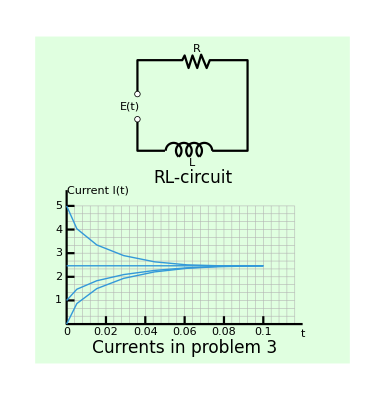

```mathematica
rangex=Range[0.4,3.3,0.1];
rangey=Range[0.5,2,0.1];
Graphics[{{LightGreen,Rectangle[{0,0},{4,4.15}]},{RGBColor[0.7,0.7,0.7],Thickness[0.001],Line[Table[{{0.4,j},{3.3,j}},{j,0.5,2,0.1}]]},{RGBColor[0.7,0.7,0.7],Thickness[0.001],Line[Table[{{j,0.5},{j,2}},{j,0.4,3.3,0.1}]]},{Thickness[0.004],Line[{{1.3,3.1},{1.3,2.7},{1.65,2.7}}]},{Thickness[0.004],Circle[{1.76,2.7},0.1,{-0.85,π}]},{Thickness[0.004],Circle[{1.89,2.7},0.1,{-0.85,π+0.85}]},{Thickness[0.004],Circle[{2.02,2.7},0.1,{-0.85,π+0.85}]},{Thickness[0.004],Circle[{2.15,2.7},0.1,{0,π+0.85}]},{Thickness[0.004],Line[{{2.25,2.7},{2.7,2.7},{2.7,3.85},{2.22,3.85},{2.18,3.75},{2.11,3.92},{2.06,3.75},{2,3.91},{1.95,3.75},{1.9,3.91},{1.87,3.85},{1.3,3.85},{1.3,3.42}}]},{Disk[{1.3,3.42},0.04]},{White,Disk[{1.3,3.42},0.03]},{Disk[{1.3,3.1},0.04]},{White,Disk[{1.3,3.1},0.03]},{Text[Style["E(t)",Medium],{1.2,3.26}]},{Text[Style["R",Medium],{2.05,3.99}]},{Text[Style["L",Medium],{1.99,2.54}]},{Text[Style["RL-circuit",17],{2,2.35}]},{Thickness[0.004],Line[{{0.4,2.2},{0.4,0.5},{3.4,0.5}}]},{Thickness[0.004],Line[{{0.4,0.8},{0.5,0.8}}]},{Thickness[0.004],Line[{{0.4,1.1},{0.5,1.1}}]},{Thickness[0.004],Line[{{0.4,1.4},{0.5,1.4}}]},{Thickness[0.004],Line[{{0.4,1.7},{0.5,1.7}}]},{Thickness[0.004],Line[{{0.4,2},{0.5,2}}]},{Thickness[0.004],Line[{{0.9,0.5},{0.9,0.6}}]},{Thickness[0.004],Line[{{1.4,0.5},{1.4,0.6}}]},{Thickness[0.004],Line[{{1.9,0.5},{1.9,0.6}}]},{Thickness[0.004],Line[{{2.4,0.5},{2.4,0.6}}]},{Thickness[0.004],Line[{{2.9,0.5},{2.9,0.6}}]},{Text[Style["0.02",Medium],{0.9,0.4}]},{Text[Style["0.04",Medium],{1.4,0.4}]},{Text[Style["0.06",Medium],{1.9,0.4}]},{Text[Style["0.08",Medium],{2.4,0.4}]},{Text[Style["0.1",Medium],{2.9,0.4}]},{Text[Style["0",Medium],{0.4,0.4}]},{RGBColor[0.2,0.6,0.85],Line[{{0.4,1.24},{2.9,1.24}}]},{RGBColor[0.2,0.6,0.85],BezierCurve[{{0.4,2},{0.55,1.1},{2.4,1.26},{2.9,1.24}}]},{RGBColor[0.2,0.6,0.85],BezierCurve[{{0.4,0.5},{0.55,1.3},{2.4,1.22},{2.9,1.24}}]},{RGBColor[0.2,0.6,0.85],BezierCurve[{{0.4,0.8},{0.55,1.23},{2.4,1.24},{2.9,1.24}}]},{Text[Style["Currents in problem 3",17],{1.9,0.2}]},{Text[Style["5",Medium],{0.3,2}]},{Text[Style["4",Medium],{0.3,1.7}]},{Text[Style["3",Medium],{0.3,1.4}]},{Text[Style["2",Medium],{0.3,1.1}]},{Text[Style["1",Medium],{0.3,0.8}]},{Text[Style["t",Medium],{3.4,0.38}]},{Text[Style["Current I(t)",Medium],{0.8,2.2}]}}]
```

When there are a lot of variables to watch, the Manipulate command is the only way I know to get an overview. The box below is based on the material at https://www.electronics-tutorials.ws/inductor/lr-circuits.html and may not agree with the text in detail.

```mathematica
eye[vee_,are_,ell_,tee_]=vee/are(1-ⅇ^(-(are tee)/ell))
```

((1-ⅇ^(-(are tee)/ell)) vee)/are

It takes some time for the current to reach its max value. From t=0.4 on in the green grid below, the circuit current is nominal.

```mathematica
Grid[Table[{tee,eye[48,10,0.25,tee]},{tee,0,0.6,0.1}],Frame->All]
```

0. | 0.
0.1 | 4.71208
0.2 | 4.79839
0.3 | 4.79997
0.4 | 4.8
0.5 | 4.8
0.6 | 4.8

```mathematica
veel[vee_,are_,ell_,tee_]=vee(ⅇ^(-(are tee)/ell))
```

ⅇ^(-(are tee)/ell) vee

```mathematica
Manipulate[Plot[{Abs[eye[vee,are,ell,tee]],Abs[veel[vee,are,ell,tee]],Abs[eye[48,10,0.25,tee]]},{tee,0,5},
PlotLegends->{"I=V/R(1-ⅇ^(-FractionBox[R t, L]))","V_L=V(ⅇ^(-FractionBox[R t, L]))","L=0.25H,R=10Ω,E=48V"},
PlotRange->{{0,0.1},{0,10}},AxesLabel->{"time","current I"},AspectRatio->0.5],{are,1,200},{ell,0.01,10} ,{vee,1,50}]
```

5.  LC-Circuit. This is an RLC-circuit with negligibly small R (analog of an undamped mass-spring system). Find the current when L=0.5 H, C = 0.005 F, and E = Sin[t V], assuming zero initial current and charge.

```mathematica
Clear["Global`*"]
```

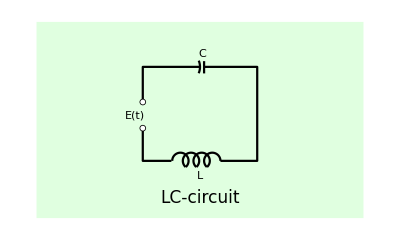

```mathematica
Graphics[{{LightGreen,Rectangle[{0,0},{4,2.4}]},{Thickness[0.004],Line[{{1.3,1.1},{1.3,0.7},{1.65,0.7}}]},{Thickness[0.004],Circle[{1.76,0.7},0.1,{-0.85,π}]},{Thickness[0.004],Circle[{1.89,0.7},0.1,{-0.85,π+0.85}]},{Thickness[0.004],Circle[{2.02,0.7},0.1,{-0.85,π+0.85}]},{Thickness[0.004],Circle[{2.15,0.7},0.1,{0,π+0.85}]},{Thickness[0.004],Line[{{2.25,0.7},{2.7,0.7},{2.7,1.85},{2.05,1.85}}]},{Thickness[0.004],Line[{{2,1.85},{1.3,1.85},{1.3,1.42}}]},{Thickness[0.004],Line[{{2.05,1.77},{2.05,1.92}}]},{Thickness[0.004],Circle[{1.8,1.85},0.2,{-0.4,0.39}]},{Disk[{1.3,1.42},0.04]},{White,Disk[{1.3,1.42},0.03]},{Disk[{1.3,1.1},0.04]},{White,Disk[{1.3,1.1},0.03]},{Text[Style["E(t)",Medium],{1.2,1.26}]},{Text[Style["C",Medium],{2.025,2.01}]},{Text[Style["L",Medium],{2.0,0.51}]},{Text[Style["LC-circuit",17],{2,0.25}]}}]
```

I found the site https://en.wikiversity.org/wiki/RLC_circuit, which has a formula which is shared by the text, i.e.
L D[q[t],{t,2}]+R D[q[t],t]-1/C q[t]=v[t]

R being negligibly small will make the first derivative term disappear, leaving

```mathematica
eqn=0.5q''[t]-1/0.005 q[t]==Sin[t V]
```

-200. q[t]+0.5 q''[t]==Sin[t V]

I will see what DSolve can do with this problem as it stands.

```mathematica
sol=DSolve[{eqn},q,t]
```

{{q→Function[{t},ⅇ^(20. t) C[1]+ⅇ^(-20. t) C[2]-(2. (0.+1. Sin[t V]))/(400.+1. V^2)]}}

DSolve pulls out a fully real solution which checks.

```mathematica
eqn/.sol//FullSimplify
```

{True}

```mathematica
ExpToTrig[ⅇ^(20. t) +ⅇ^(-20. t)]
```

2 Cosh[20. t]

So to clean it up,

```mathematica
2 Cosh[20 t]-(2 Sin[t V])/(400+ V^2)
```

Which doesn’t look too hairy, though not the same as the text answer.

Example 1 on p. 96 of the text could repay close study on this problem. Roots of the characteristic equation, along with reactance, can yield the coefficients of the particular equation after some work. One thing that bothers me is the vagueness of the voltage function. Maybe something cancels out to make the answer come out so neat. The text answer, by the way, is (I=2(Cos[t] - Cos[20 t]))/399.

Freezing some parameter values in order to take a look at the thing.

The plot does not look like figure 63 on p. 97.

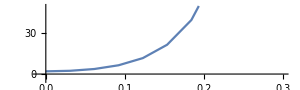

```mathematica
Plot[2 Cosh[20 t]-(2 Sin[t])/401,{t,0,100},ImageSize->300,AspectRatio->.3,PlotRange->{{-0.01,0.3},{-5,50}}]
```

7 - 18 General RLC-circuits

7.  Tuning. In tuning a sterio system to a radio station, we adjust the tuning control (turn a knob) that changes C (or perhaps L) in an RLC-circuit so that the amplitude of the steady-state current, numbered line (5), p. 95 becomes maximum. For what C will this happen?

It is where the particular solution of the homogeneous equation is maximized. Numbered line (5) looks like

I_p(t)=I_0 Sin[ω t-θ]

The quantity θ is known as the phase lag, and, I suppose, the signal is best, I_p maximized, when θ equals zero.

8 - 14 Find the steady-state current in the RLC-circuit in the figure below for the given data.

9.  R = 4 Ω, L = 0.1 H, C = 0.05 F, E = 110 V

L D[q[t],{t,2}]+R D[q[t],t]-1/C q[t]=v[t]

```mathematica
eqn=0.1q''[t]+4q'[t]-1/0.05 q[t]==110
```

-20. q[t]+4 q'[t]+0.1 q''[t]==110

```mathematica
sol=DSolve[eqn,q,t]
```

{{q→Function[{t},-5.5+ⅇ^(-44.4949 t) C[1]+ⅇ^(4.4949 t) C[2]]}}

If C[1]=C[2]=0, then the green cell above matches the text answer.

11.  R = 12 Ω, L = 0.4 H, C = 1/80F, E = 220 Sin[10 t] V

```mathematica
eqn=0.4q''[t]+12q'[t]-80q[t]==220Sin[10 t]
```

-80 q[t]+12 q'[t]+0.4 q''[t]==220 Sin[10 t]

```mathematica
sol=DSolve[eqn,q,t]
```

{{q→Function[{t},ⅇ^(-35.6155 t) C[1]+ⅇ^(5.61553 t) C[2]+0.0974775 ⅇ^(-8.88178×10^-16 t) (-10.4039 Cos[10. t]+1. ⅇ^(8.88178×10^-16 t) Cos[10. t]-5.84233 Sin[10. t]-(3.56155+1.18695×10^-16 ⅈ) ⅇ^(8.88178×10^-16 t) Sin[10. t])]}}

```mathematica
FullSimplify[ⅇ^(-35.6155281280883 t) C[1]+ⅇ^(5.615528128088303 t) C[2]+0.09747747404159644 ⅇ^(-8.881784197001252*^-16 t) (-10.403882032022072 Cos[10. t]+1. ⅇ^(8.881784197001252*^-16 t) Cos[10. t]-5.842329219213245 Sin[10. t]-(3.56155281280883+1.186954912693127*^-16 ⅈ) ⅇ^(8.881784197001252*^-16 t) Sin[10. t])/.{C[1]->0,C[2]->0}]
```

ⅇ^(-8.88178×10^-16 t) ((-1.01414+0.0974775 ⅇ^(8.88178×10^-16 t)) Cos[10. t]+(-0.569495-(0.347171+1.15701×10^-17 ⅈ) ⅇ^(8.88178×10^-16 t)) Sin[10. t])

```mathematica
FullSimplify[ⅇ^(-8.881784197001252*^-16 t) ((-1.0141441407082632+0.09747747404159644 ⅇ^(8.881784197001252*^-16 t)) Cos[10. t]+(-0.5694954948083195-(0.3471711718583475+1.1570136669058967*^-17 ⅈ) ⅇ^(8.881784197001252*^-16 t)) Sin[10. t])]
```

ⅇ^(-8.88178×10^-16 t) ((-1.01414+0.0974775 ⅇ^(8.88178×10^-16 t)) Cos[10. t]+(-0.569495-(0.347171+1.15701×10^-17 ⅈ) ⅇ^(8.88178×10^-16 t)) Sin[10. t])

Dump the imaginary.

```mathematica
ⅇ^(-8.881784197001252*^-16 t) ((-1.0141441407082632+0.09747747404159644 ⅇ^(8.881784197001252*^-16 t)) Cos[10. t]+(-0.5694954948083195) ⅇ^(8.881784197001252*^-16 t)) Sin[10. t])
```

Try to plot it.

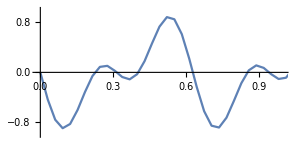

```mathematica
Plot[ⅇ^(-8.881784197001252*^-16 t) ((-1.0141441407082632+0.09747747404159644 ⅇ^(8.881784197001252*^-16 t)) Cos[10. t]+(-0.5694954948083195) ⅇ^(8.881784197001252*^-16 t)) Sin[10. t],{t,0,100},ImageSize->300,AspectRatio->.5,PlotRange->{{-0.01,1},{-1,1}}]
```

By the way, the trig elements in the text answer are present in the yellow. The text answer is I=5.5Cos[10 t]+16.5 Sin[10 t] amperes.

13.  R = 12, L = 1.2 H, C = 20/3*10^-3 F, E = 12,000 Sin[25 t] V

C=20/3*1/1000=20/3000=2/300

```mathematica
eqn=1.2q''[t]+12 q'[t]-300/2 q[t]==12000Sin[25 t]
```

-150 q[t]+12 q'[t]+1.2 q''[t]==12000 Sin[25 t]

```mathematica
sol=DSolve[eqn,q,t]
```

{{q→Function[{t},ⅇ^(-17.2474 t) C[1]+ⅇ^(7.24745 t) C[2]-(4.-7.08198×10^-16 ⅈ) ((1.+0. ⅈ) Cos[25. t]+(3.+5.31148×10^-16 ⅈ) Sin[25. t])]}}

```mathematica
(ⅇ^(-17.24744871391589 t) +ⅇ^(7.24744871391589 t) -(4.) Cos[25. t]+(3.) Sin[25. t])/.t->0.5
```

33.2869

The next few cells try out the Assini method of undetermined coefficients.

```mathematica
hAndp[odeH_,rhs_,y_,x_]:=Module[{wronskian,u1,u2,solH,y1,y2,leadingC},leadingC=Cases[odeH,c_ y''[x]:>c];
leadingC=If[leadingC==={},1,First@leadingC];
solH=(y[x]/.First@DSolve[odeH==0,y[x],x]);
{y1,y2}=solH/.C[1] y1_+C[2] y2_:>{y1,y2};(*basis solutions*)wronskian=Det[{{y1,y2},{D[y1,x],D[y2,x]}}];
u1=-Integrate[y2 rhs/(leadingC*wronskian),x];
u2=Integrate[y1 rhs/(leadingC*wronskian),x];
{solH,Simplify[y1 u1+y2 u2]}];
```

```mathematica
odeH=-150 q[t]+12 q'[t]+1.2 q''[t];
rhs=12000 Sin[25 t];
```

```mathematica
{yh,yp}=hAndp[odeH,rhs,q,t]
```

{ⅇ^(-17.2474 t) C[1]+ⅇ^(7.24745 t) C[2],(-4.-7.08198×10^-16 ⅈ) Cos[25. t]-12. Sin[25. t]}

```mathematica
fullSolution=yh+yp
```

ⅇ^(-17.2474 t) C[1]+ⅇ^(7.24745 t) C[2]-(4.+7.08198×10^-16 ⅈ) Cos[25. t]-12. Sin[25. t]

Trying to clean and standardize a little.

```mathematica
mfs=ⅇ^(-17.24744871391589 t) +ⅇ^(7.24744871391589 t)-(4.) Cos[25. t]-12. Sin[25. t]
```

ⅇ^(-17.2474 t)+ⅇ^(7.24745 t)-4. Cos[25. t]-12. Sin[25. t]

```mathematica
mfs1=mfs/.t->0.5
```

34.2817

```mathematica
(ⅇ^(-5t)(Cos[10 t]+Sin[10t])-400Cos[25 t]+200Sin[25 t])/.t->0.5
```

-412.439

As can be seen above, the text answer (pink) is not achieved.

15. Cases of damping. What are the conditions for an RLC-circuit to be (I) overdamped, (II) critically damped, (III) underdamped? What is the critical resistance R_crit (the analog of the critical damping constant 2 √(m k) ?

16 - 18 Solve the initial value problem for the RLC-circuit shown below, with the given data, assuming zero initial current and charge. Graph or sketch the solution.

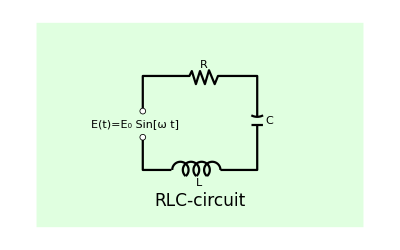

```mathematica
Graphics[{{LightGreen,Rectangle[{0,0},{4,2.5}]},{Thickness[0.004],Line[{{1.3,1.1},{1.3,0.7},{1.65,0.7}}]},{Thickness[0.004],Circle[{1.76,0.7},0.1,{-0.85,π}]},{Thickness[0.004],Circle[{1.89,0.7},0.1,{-0.85,π+0.85}]},{Thickness[0.004],Circle[{2.02,0.7},0.1,{-0.85,π+0.85}]},{Thickness[0.004],Circle[{2.15,0.7},0.1,{0,π+0.85}]},{Thickness[0.004],Line[{{2.25,0.7},{2.7,0.7},{2.7,1.25}}]},{Thickness[0.004],Line[{{2.63,1.25},{2.77,1.25}}]},{Thickness[0.004],Circle[{2.7,1.5},0.15,{-π/2-0.5,-π/2+0.5}]},{Thickness[0.004],Line[{{2.7,1.35},{2.7,1.85},{2.22,1.85},{2.18,1.75},{2.11,1.92},{2.06,1.75},{2,1.91},{1.95,1.75},{1.9,1.91},{1.87,1.85},{1.3,1.85},{1.3,1.42}}]},{Disk[{1.3,1.42},0.04]},{White,Disk[{1.3,1.42},0.03]},{Disk[{1.3,1.1},0.04]},{White,Disk[{1.3,1.1},0.03]},{Text[Style["E(t)=E_0 Sin[ω t]",Medium],{1.2,1.26}]},{Text[Style["R",Medium],{2.05,1.99}]},{Text[Style["L",Medium],{1.99,0.54}]},{Text[Style["RLC-circuit",17],{2,0.32}]},{Text[Style["C",Medium],{2.85,1.3}]}},Axes->False]
```

17.  R = 6 Ω, L = 1 H, C = 0.04 F, E = 600(Cos[t] + 4 Sin[t])V

L D[q[t],{t,2}]+R D[q[t],t]-1/C q[t]=v[t]

```mathematica
Clear["Global`*"]
```

```mathematica
eqn=1q''[t]+6q'[t]-25q[t]==600(Cos[t]+4Sin[t])
```

-25 q[t]+6 q'[t]+q''[t]==600 (Cos[t]+4 Sin[t])

```mathematica
sol=DSolve[eqn,q,t]
```

{{q→Function[{t},ⅇ^((-3-√34) t) C[1]+ⅇ^((-3+√34) t) C[2]+(300 (25 Cos[t]+49 Sin[t]))/((-22+3 √34) (22+3 √34))]}}

The solution found by Mathematica checks.

```mathematica
eqn/.sol//Simplify
```

{True}

```mathematica
(300 (25 Cos[t]+49 Sin[t]))/((-22+3 √34) (22+3 √34))/.t->0.5
```

-76.5698

```mathematica
(ⅇ^(-3t)(-100Cos[4t]+75Sin[4t])+100Cos[t])/.t->0.5
```

112.261

The text answer (pink) was not found.

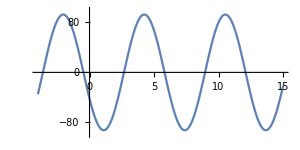

```mathematica
Plot[(300 (25 Cos[t]+49 Sin[t]))/((-22+3 √34) (22+3 √34)),{t,-4,15},ImageSize->300,AspectRatio->.5,PlotRange->{{-4,15},{-100,100}}]
```